# Enhancing the SpokenString function output based on the input symbolic structure

Renan Germano

Science

When dealing with graphs and images, the current SpokenString function returns a not significant text to the describe the input. The objective of the present project is to enhance this output by developing an algorithm that is capable of  better describing the input, based on its symbolic structure. Thinking about accessibility for visually impaired, this text could be used as an automatic generated alternative description for images and related contents.

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

### Some Experiments

```mathematica
?WolframLanguageData
```

```mathematica
wlSymbols = WolframLanguageData[];
```

```mathematica
wlSymbols//Length
```

5605

```mathematica
wfSampleSymbols = WolframLanguageData["SampleEntities"]
```

{Integrate,GroebnerBasis,Association,ParametricPlot,EntityValue,Binomial,ListConvolve,NestList}

```mathematica
WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
#->EntityValue[#, EntityProperty["WolframLanguageSymbol", "FunctionalityAreas"]]&/@wfSampleSymbols//TableForm
```

Integrate→{CalculusSymbols}
GroebnerBasis→{PolynomialSymbols}
Association→{AssociationSymbols}
ParametricPlot→{PlottingSymbols}
EntityValue→{EntitySymbols}
Binomial→{BasicSymbols}
ListConvolve→{ListSymbols}
NestList→{CodeActionSymbols}

```mathematica
Select[wfSampleSymbols, (First@EntityValue[#, EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]=="BasicSymbols")&]
```

{Binomial}

```mathematica
Select[wfSampleSymbols, With[
{functionality=EntityValue[#, EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]},
Length@functionality==1&&First@functionality=="BasicSymbols"
]&
]
```

{Binomial}

```mathematica
Select[wfSampleSymbols, With[
{functionality=EntityValue[#, EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]},
Length@functionality==1 && First@functionality=="ListSymbols"
]&
]
```

{ListConvolve}

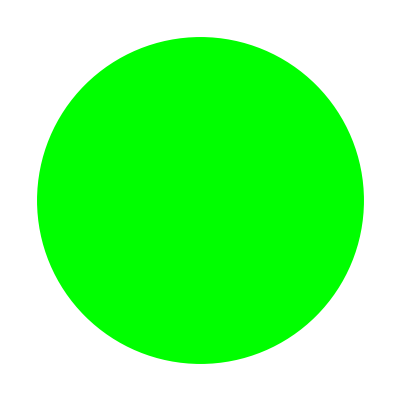
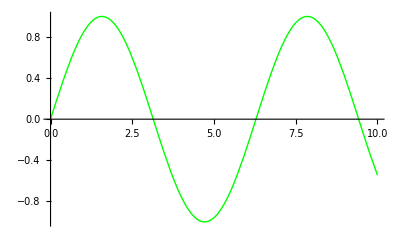
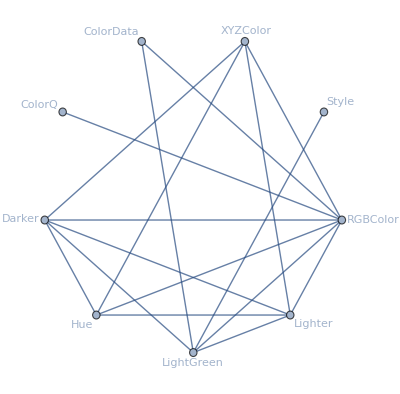
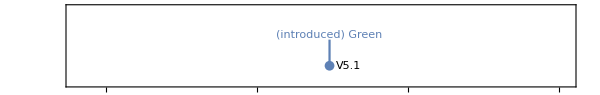
attributes→{Protected}
character count→5
common option values→Missing[NotApplicable]
date introduced→Day: Mon 25 Oct 2004
date last modified→Missing[NotAvailable]
dates modified→Missing[NotAvailable]
documentation basic examples→{{Graphics[{Green,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Green],-Graphics-,Graphics3D[{Green,Sphere[]}],-Graphics3D-}}
documentation example counts→{BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs→{BasicExamples→{{Graphics[{Green,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Green],Graphics3D[{Green,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text→{BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes→{Wolfram Language autoevaluating symbols}
eponymous people→{}
equal-precedence symbols→Missing[NotApplicable]
external links→{}
frequencies of usage→{All→0.000145182,StackExchange→0.00072014,TypicalProductionCode→0.000376487,WolframAlphaCodebase→2.99023×10^-6,WolframDemonstrations→0.000898782,WolframDocumentation→0.000683278}
full version introduced→5.1
full version last modified→Missing[NotAvailable]
full versions modified→Missing[NotAvailable]
functionality areas→{ColorSymbols}
symbol background→Green is a symbol that represents the color green in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Green,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Green]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Green]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Green]).
Green is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[0,1,0].
Named symbols for other colors include Red, Blue, Black, White, Cyan, Gray, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
keyboard shortcuts→Missing[NotAvailable]
link trails→{{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Green},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Green},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Green}}
memberships→{Wolfram Language autoevaluating symbols}
name→Green
option names→{}
options→{}
plaintext usage→Green represents the color green in graphics or style specifications.
precedence ranks→Missing[NotApplicable]
ranks of usage→{All→198,StackExchange→125,TypicalProductionCode→172,WolframAlphaCodebase→675,WolframDemonstrations→96,WolframDocumentation→125}
related entities→{green}
related guide pages→{Colorspaclet:guide/Colors,Graphics Directivespaclet:guide/GraphicsDirectives,Color Processingpaclet:guide/ColorProcessing}
related symbols→{LightGreen,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph→-Graphics-
relationship graph→-Graphics-
short notations→Missing[NotApplicable]
subject classifications→Missing[NotAvailable]
symbols linking to→{ColorQ,Hue,LightGreen,RGBColor,XYZColor}
symbols using as attribute→{}
symbols using as option→{}
text strings→{Green represents the color green in graphics or style specifications.,Green is equivalent to RGBColor[0,1,0].,Green is a symbol that represents the color green in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Green,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Green]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Green]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Green]).,Green is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[0,1,0].,Named symbols for other colors include Red, Blue, Black, White, Cyan, Gray, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline→-Graphics-
timeline events→Day: Mon 25 Oct 2004Green
translations→{Simplified Chinese→绿色,Traditional Chinese→綠色,French→vert,German→grün,Modern Greek→πράσινο,Japanese→緑,Korean→녹색,Lithuanian→žalias,Polish→zielony,Portuguese→verde,Russian→зелёный,Spanish→verde,Ukrainian→зелений,Vietnamese→xanh lá}
typeset usage→Green represents the color green in graphics or style specifications. 
URL→http://reference.wolfram.com/language/ref/Green.html
version introduced→5.1
version last modified→Missing[NotAvailable]
versions modified→Missing[NotAvailable]
Wolfram documentation link→Greenpaclet:ref/Green

```mathematica
#->WolframLanguageData["Green", #]&/@%//TableForm
```

```mathematica
Entity["WolframLanguageSymbol","Green"]//Symbol[EntityValue[#,EntityProperty["WolframLanguageSymbol","Name"]]]&//InputForm//TextForm
```

RGBColor[0, 1, 0]

```mathematica
Green//ColorArrayForm
```

ColorArrayForm[RGBColor[0, 1, 0]]

```mathematica
?*Form
```

```mathematica
ColorData/@ColorData[]//TableForm
```

```mathematica
colors = ColorData["HTML", "ColorList"]
```

{RGBColor[0.9411764705882353, 0.9725490196078431, 1.],RGBColor[0.9803921568627451, 0.9215686274509803, 0.8431372549019608],RGBColor[0, 1., 1.],RGBColor[0.4980392156862745, 1., 0.8313725490196078],RGBColor[0.9411764705882353, 1., 1.],RGBColor[0.9607843137254902, 0.9607843137254902, 0.8627450980392157],RGBColor[1., 0.8941176470588235, 0.7686274509803921],RGBColor[0, 0, 0],RGBColor[1., 0.9215686274509803, 0.803921568627451],RGBColor[0, 0, 1.],RGBColor[0.5411764705882353, 0.16862745098039217, 0.8862745098039215],RGBColor[0.6470588235294118, 0.16470588235294117, 0.16470588235294117],RGBColor[0.8705882352941177, 0.7215686274509804, 0.5294117647058824],RGBColor[0.37254901960784315, 0.6196078431372549, 0.6274509803921569],RGBColor[0.4980392156862745, 1., 0],RGBColor[0.8235294117647058, 0.4117647058823529, 0.11764705882352941],RGBColor[1., 0.4980392156862745, 0.3137254901960784],RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824],RGBColor[1., 0.9725490196078431, 0.8627450980392157],RGBColor[0.8627450980392157, 0.0784313725490196, 0.23529411764705882],RGBColor[0, 1., 1.],RGBColor[0, 0, 0.5450980392156862],RGBColor[0, 0.5450980392156862, 0.5450980392156862],RGBColor[0.7215686274509804, 0.5254901960784314, 0.043137254901960784],RGBColor[0.6627450980392157, 0.6627450980392157, 0.6627450980392157],RGBColor[0, 0.39215686274509803, 0],RGBColor[0.7411764705882353, 0.7176470588235294, 0.4196078431372549],RGBColor[0.5450980392156862, 0, 0.5450980392156862],RGBColor[0.3333333333333333, 0.4196078431372549, 0.1843137254901961],RGBColor[1., 0.5490196078431373, 0],RGBColor[0.6, 0.19607843137254902, 0.8],RGBColor[0.5450980392156862, 0, 0],RGBColor[0.9137254901960784, 0.5882352941176471, 0.4784313725490196],RGBColor[0.5607843137254902, 0.7372549019607844, 0.5607843137254902],RGBColor[0.2823529411764706, 0.2392156862745098, 0.5450980392156862],RGBColor[0.1843137254901961, 0.30980392156862746, 0.30980392156862746],RGBColor[0, 0.807843137254902, 0.8196078431372549],RGBColor[0.580392156862745, 0, 0.8274509803921568],RGBColor[1., 0.0784313725490196, 0.5764705882352941],RGBColor[0, 0.7490196078431373, 1.],RGBColor[0.4117647058823529, 0.4117647058823529, 0.4117647058823529],RGBColor[0.11764705882352941, 0.5647058823529412, 1.],RGBColor[0.6980392156862745, 0.13333333333333333, 0.13333333333333333],RGBColor[1., 0.9803921568627451, 0.9411764705882353],RGBColor[0.13333333333333333, 0.5450980392156862, 0.13333333333333333],RGBColor[1., 0, 1.],RGBColor[0.8627450980392157, 0.8627450980392157, 0.8627450980392157],RGBColor[0.9725490196078431, 0.9725490196078431, 1.],RGBColor[1., 0.8431372549019608, 0],RGBColor[0.8549019607843137, 0.6470588235294118, 0.12549019607843137],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0, 0.5019607843137255, 0],RGBColor[0.6784313725490196, 1., 0.1843137254901961],RGBColor[0.9411764705882353, 1., 0.9411764705882353],RGBColor[1., 0.4117647058823529, 0.7058823529411764],RGBColor[0.803921568627451, 0.3607843137254902, 0.3607843137254902],RGBColor[0.29411764705882354, 0, 0.5098039215686274],RGBColor[1., 1., 0.9411764705882353],RGBColor[0.9411764705882353, 0.9019607843137255, 0.5490196078431373],RGBColor[0.9019607843137255, 0.9019607843137255, 0.9803921568627451],RGBColor[1., 0.9411764705882353, 0.9607843137254902],RGBColor[0.48627450980392156, 0.9882352941176471, 0],RGBColor[1., 0.9803921568627451, 0.803921568627451],RGBColor[0.6784313725490196, 0.8470588235294118, 0.9019607843137255],RGBColor[0.9411764705882353, 0.5019607843137255, 0.5019607843137255],RGBColor[0.8784313725490196, 1., 1.],RGBColor[0.9803921568627451, 0.9803921568627451, 0.8235294117647058],RGBColor[0.8274509803921568, 0.8274509803921568, 0.8274509803921568],RGBColor[0.5647058823529412, 0.9333333333333333, 0.5647058823529412],RGBColor[1., 0.7137254901960784, 0.7568627450980392],RGBColor[1., 0.6274509803921569, 0.4784313725490196],RGBColor[0.12549019607843137, 0.6980392156862745, 0.6666666666666666],RGBColor[0.5294117647058824, 0.807843137254902, 0.9803921568627451],RGBColor[0.4666666666666667, 0.5333333333333333, 0.6],RGBColor[0.6901960784313725, 0.7686274509803921, 0.8705882352941177],RGBColor[1., 1., 0.8784313725490196],RGBColor[0, 1., 0],RGBColor[0.19607843137254902, 0.803921568627451, 0.19607843137254902],RGBColor[0.9803921568627451, 0.9411764705882353, 0.9019607843137255],RGBColor[1., 0, 1.],RGBColor[0.5019607843137255, 0, 0],RGBColor[0.4, 0.803921568627451, 0.6666666666666666],RGBColor[0, 0, 0.803921568627451],RGBColor[0.7294117647058823, 0.3333333333333333, 0.8274509803921568],RGBColor[0.5764705882352941, 0.4392156862745098, 0.8588235294117647],RGBColor[0.23529411764705882, 0.7019607843137254, 0.44313725490196076],RGBColor[0.4823529411764706, 0.40784313725490196, 0.9333333333333333],RGBColor[0, 0.9803921568627451, 0.6039215686274509],RGBColor[0.2823529411764706, 0.8196078431372549, 0.8],RGBColor[0.7803921568627451, 0.08235294117647059, 0.5215686274509804],RGBColor[0.09803921568627451, 0.09803921568627451, 0.4392156862745098],RGBColor[0.9607843137254902, 1., 0.9803921568627451],RGBColor[1., 0.8941176470588235, 0.8823529411764706],RGBColor[1., 0.8941176470588235, 0.7098039215686275],RGBColor[1., 0.8705882352941177, 0.6784313725490196],RGBColor[0, 0, 0.5019607843137255],RGBColor[0.9921568627450981, 0.9607843137254902, 0.9019607843137255],RGBColor[0.5019607843137255, 0.5019607843137255, 0],RGBColor[0.4196078431372549, 0.5568627450980392, 0.13725490196078433],RGBColor[1., 0.6470588235294118, 0],RGBColor[1., 0.27058823529411763, 0],RGBColor[0.8549019607843137, 0.4392156862745098, 0.8392156862745098],RGBColor[0.9333333333333333, 0.9098039215686274, 0.6666666666666666],RGBColor[0.596078431372549, 0.984313725490196, 0.596078431372549],RGBColor[0.6862745098039216, 0.9333333333333333, 0.9333333333333333],RGBColor[0.8588235294117647, 0.4392156862745098, 0.5764705882352941],RGBColor[1., 0.9372549019607843, 0.8352941176470589],RGBColor[1., 0.8549019607843137, 0.7254901960784313],RGBColor[0.803921568627451, 0.5215686274509804, 0.24705882352941178],RGBColor[1., 0.7529411764705882, 0.796078431372549],RGBColor[0.8666666666666667, 0.6274509803921569, 0.8666666666666667],RGBColor[0.6901960784313725, 0.8784313725490196, 0.9019607843137255],RGBColor[0.5019607843137255, 0, 0.5019607843137255],RGBColor[1., 0, 0],RGBColor[0.7372549019607844, 0.5607843137254902, 0.5607843137254902],RGBColor[0.2549019607843137, 0.4117647058823529, 0.8823529411764706],RGBColor[0.5450980392156862, 0.27058823529411763, 0.07450980392156863],RGBColor[0.9803921568627451, 0.5019607843137255, 0.44705882352941173],RGBColor[0.9568627450980391, 0.6431372549019607, 0.3764705882352941],RGBColor[0.1803921568627451, 0.5450980392156862, 0.3411764705882353],RGBColor[1., 0.9607843137254902, 0.9333333333333333],RGBColor[0.6274509803921569, 0.32156862745098036, 0.1764705882352941],RGBColor[0.7529411764705882, 0.7529411764705882, 0.7529411764705882],RGBColor[0.5294117647058824, 0.807843137254902, 0.9215686274509803],RGBColor[0.4156862745098039, 0.3529411764705882, 0.803921568627451],RGBColor[0.4392156862745098, 0.5019607843137255, 0.5647058823529412],RGBColor[1., 0.9803921568627451, 0.9803921568627451],RGBColor[0, 1., 0.4980392156862745],RGBColor[0.27450980392156865, 0.5098039215686274, 0.7058823529411764],RGBColor[0.8235294117647058, 0.7058823529411764, 0.5490196078431373],RGBColor[0, 0.5019607843137255, 0.5019607843137255],RGBColor[0.8470588235294118, 0.7490196078431373, 0.8470588235294118],RGBColor[1., 0.38823529411764707, 0.2784313725490196],RGBColor[0.25098039215686274, 0.8784313725490196, 0.8156862745098039],RGBColor[0.9333333333333333, 0.5098039215686274, 0.9333333333333333],RGBColor[0.9607843137254902, 0.8705882352941177, 0.7019607843137254],RGBColor[1., 1., 1.],RGBColor[0.9607843137254902, 0.9607843137254902, 0.9607843137254902],RGBColor[1., 1., 0],RGBColor[0.6039215686274509, 0.803921568627451, 0.19607843137254902]}

```mathematica
allColors = EntityValue["Color", "Entities"]
```

{HTML peach,Colorado Yellow,Condor Yellow,Sahara,Ceylon Gold Metallic,Sienna Brown Metallic,Sierra Beige,Topaz Brown Metallic,Iberian Red,Ruby Red Metallic,Coral,Malaga Red,Inka (Orange),Verona Red (Light),Granite Metallic,Madeira,Phoenix Orange,Riviera Blue,Fjord Blue Metallic,Night Blue Metallic,Atlantic Blue,Baikal Metallic,Stato Blue (Pastel),Arctic Blue Metallic,Henna Red,Brodeaux Red,Ocean Blue,Anthracite Gray Metallic,Bristol Gray (Light),New Polaris Metallic,New Polaris Metallic,New Polaris Metallic,Green,Tuerkis Metallic,Tundra Green Metallic,Golf (Green),Golf (Green),Agave Green,Taiga Metallic (Light Green),Reseda Green Metallic,Amazon Green,Jade Green,Mint Green,Chamonix White,Black,Graphite Metallic,Gazelle Beize,Cinnabar,Bronzit Beige Metallic,Biscay Blue,Green,Sepia Brown,Cashmere Metallic,Alpine White,Alpine White,Safari Beige,Corona Yellow,Sapphire Blue Metallic,Strato Blue Metallic,Ascot Gray Metallic,Cypress Green Metallic,Brazil Brown Metallic,Chestnut Red Metallic,Bahama Metallic,Opal Green Metallic,Lapis Blue,Saturn Blue,Agate Green Metallic,Baltic Blue Metallic,Diamond Black Metallic,Delphin Metallic,Cosmos Blue Metallic,Savannah Beige,Cirrus Blue Metallic,Sable Brown Metallic,Royal Blue Metallic,Burgundy Metallic,Salmon Silver Metallic,Alpine White II,Luxor Beige Metallic,Granite Silver Metallic,Nogarosilver Metallic,Sterling Silver Metallic,Calypso Red Pearl,Calypso Red Pearl,Brocade Red Pearl,Dark Blue,Laguna Green Pearl Metallic,Dakar Yellow,Arctic Gray Metallic,Island Green Metallic,Mugello Red,Boston Green Metallic,Avus Blue Pearl,Glacier Blue Metallic,Sienna Red Pearl Metallic,Savannah Beige Metallic,Daytona Violet Pearl Metallic,Cordoba Red Metallic,Mauritius Blue Pearl,Morea Green Metallic,Malediven Blue Metallic,Azure Blue Metallic,Samoa Blue Metallic,Montreal Blue Pearl,Techno Violet Pearl,Alpine White III,Alpine White III,Cashmere Beige Metallic,Madeira Violet Pearl,Cosmos Black Pearl Metallic,Cosmosschwarz Metallic,Violet Black,Atlanta Blue Metallic,Dark Green II,Bright Red,Arctic Silver Metallic,Arktissilber Metallic,Fjord Grey Pearl,British Racing Green,Bright Red,Brt Red,Hellrot,Violet Red,Orient Blue Metallic,Nautical Green,Oxford Green Pearl Metallic,Turquoise Green,Violet Red II,Volcano Gray,Mojave Brown Metallic,Glacier Green Metallic,Estoril Blue Metallic,Aegan Metallic,Dakargelb,Dakar Yellow II,Aspen Silver Metallic,Canyon Red Metallic,Navarra Violet Metallic,Aubergine,Olive Metallic,Olive Metallic,Ascot Green Metallic,Titanium Silver Metallic,Titan Silver Metallic,Titan Silver Metallic,Titan Silver Metallic,Byzanz Metallic,Vermont Green Metallic,Sierra Red Metallic,Evergreen,Sorrent Blue Metallic,Siena Red II Metallic,Biarritz Blue Metallic,Topaz Blue Metallic,Brick Red,Imala Red,Alaska Blue Metallic,Steel Blue Metallic,Dark Grey Metallic (wheel),Light Yellow Metallic,Lemans Blue Metallic,Le mans Blue Metallic,Fern Green Metallic,Royal Red Metallic,Original Bumper Cover,Sea Green Metallic,Anthracite Metallic,Kiruna Violet Metallic,Steel Gray Metallic,Imola Red,Imola Red II,Orinocco Metallic,Pearl Beige Metallic,Bright Red II,Carbon Black Metallic,Carbon Black Metallic,Carbon Black Metallic,Carbon Black Metallic,Impala Brown Metallic,Silverstone Metallic,Neon Yellow,Oxford Green Metallic,Oxfordgruen II Pearl,Apricot Metallic,Mahagony Metallic,Electric Red,Stratusgrau Metallic,Stratus Gray Metallic,Stratus Metallic,Grey Green Metallic,Sahara Beige Metallic,Phoenix Yellow Metallic,Criollo Metallic,Laguna Seca,Slate Green Metallic,Aqua Metallic,Midnight Blue Metallic,Pistachio Green Metallic,Black (matt),Flamenco Red Metallic,Sterling Gray Metallic,Sterling Pearl Gray Metallic,Black Saphire Metallic,Black Sapphire Metallic,Kalahari Beige Metallic,Kalaharibeige Metallic,Kalahari Beige Metallic,Toledoblau Metallic,Toledo Blue Metallic,Toledo Blue Metallic,Sonderlackierung Metallic,Alpina Blue Metallic,Bluewater Metallic,Pacific Blue,Caribbean Blue,Night Blue Metallic,Velvet Blue Metallic,Baikal Metallic,Jet Black,Jet Black,Hellgrau (matt),Dark Gray (matt Dupont P2279),Cortinagrau,Anthrazit (matt),Laser Blue Metallic,Mocha Brown Metallic,Titanium Gray Metallic,Chiareto Red Metallic,Bluewater Metallic,Blue Water Metallic,Tourmaline Violet Metallic,New Polaris Metallic,New Polaris Metallic,Turquoise Metallic,Merlot Red Metallic,Urban Green,Copper Metallic,Mysticblau Metallic,Mystic Blue Metallic,Silbergrau Metallic,Silver Grey Metallic,Silver Gray Metallic,Amethyst Gray Metallic,Diamant Metallic,Highland Green Metallic,Highland Green Metallic,Atlantic Blue Metallic,Atlantic Blue Metallic,Mineral Silver Metallic,Mineral Silver Metallic,Maldives Blue Metallic,Havanna Metallic,Havanna Metallic,Mojave Metallic,Havanna Metallic,Havanna Metallic,Havanna Metallic,Quartz Blue Metallic,Quarzblau Metallic,Nautica Blue Metallic,Sparkling Graphite Metallic,Sparkling Graphite Metallic,Sparkling Graphit Metallic,Sparklng Graphte Metallic,9856,Pantone 7516 PC,Pantone 7516 UP,Pantone 7517 C,Pantone 7517 EC,Pantone 7517 PC,Pantone 7517 UP,Pantone 7518 C,Pantone 7518 EC,Pantone 7518 PC,Pantone 7518 UP,Pantone 7519 C,Pantone 7519 EC,Pantone 7519 PC,Pantone 7519 UP,Pantone 7520 C,Pantone 7520 EC,Pantone 7520 PC,Pantone 7520 UP,Pantone 7521 C,Pantone 7521 EC,Pantone 7521 PC,Pantone 7521 UP,Pantone 7522 C,Pantone 7522 EC,Pantone 7522 PC,Pantone 7522 UP,Pantone 7523 C,Pantone 7523 EC,Pantone 7523 PC,Pantone 7523 UP,Pantone 7524 C,Pantone 7524 EC,Pantone 7524 PC,Pantone 7524 UP,Pantone 7525 C,Pantone 7525 EC,Pantone 7525 PC,Pantone 7525 UP,Pantone 7526 C,Pantone 7526 EC,Pantone 7526 PC,Pantone 7526 UP,Pantone 7527 C,Pantone 7527 EC,Pantone 7527 PC,Pantone 7527 UP,Pantone 7528 C,Pantone 7528 EC,Pantone 7528 PC,Pantone 7528 UP,Pantone 7529 C,Pantone 7529 EC,Pantone 7529 PC,Pantone 7529 UP,Pantone 7530 C,Pantone 7530 EC,Pantone 7530 PC,Pantone 7530 UP,Pantone 7531 C,Pantone 7531 EC,Pantone 7531 PC,Pantone 7531 UP,Pantone 7532 C,Pantone 7532 EC,Pantone 7532 PC,Pantone 7532 UP,Pantone 7533 C,Pantone 7533 EC,Pantone 7533 PC,Pantone 7533 U,Pantone 7533 UP,Pantone 7534 C,Pantone 7534 EC,Pantone 7534 PC,Pantone 7534 UP,Pantone 7535 C,Pantone 7535 EC,Pantone 7535 PC,Pantone 7535 UP,Pantone 7536 C,Pantone 7536 EC,Pantone 7536 PC,Pantone 7536 UP,Pantone 7537 C,Pantone 7537 EC,Pantone 7537 PC,Pantone 7537 UP,Pantone 7538 C,Pantone 7538 EC,Pantone 7538 PC,Pantone 7538 UP,Pantone 7539 C,Pantone 7539 EC,Pantone 7539 PC,Pantone 7539 UP,Pantone 7540 C,Pantone 7540 EC,Pantone 7540 PC,Pantone 7540 UP,Pantone 7541 C,Pantone 7541 EC,Pantone 7541 PC,Pantone 7541 UP,Pantone 7542 C,Pantone 7542 EC,Pantone 7542 PC,Pantone 7542 UP,Pantone 7543 C,Pantone 7543 EC,Pantone 7543 PC,Pantone 7543 UP,Pantone 7544 C,Pantone 7544 EC,Pantone 7544 PC,Pantone 7544 UP,Pantone 7545 C,Pantone 7545 EC,Pantone 7545 PC,Pantone 7545 UP,Pantone 7546 C,Pantone 7546 EC,Pantone 7546 PC,Pantone 7546 UP,Pantone 7547 C,Pantone 7547 EC,Pantone 7547 PC,Pantone 7547 UP,Pantone 032 C,Pantone 2X 327,Pantone 2X 471,Pantone 2X 485,Pantone Black C,Pantone Black PC,Pantone Cool Gray 2,Pantone Cool Gray 5,Pantone Cool Gray 6,Pantone Cool Gray 9,Pantone Cool Gray 10,Pantone Green C,Pantone Green PC,Pantone Purple C,Pantone Purple PC,Pantone Red 032,Pantone Reflex Blue,Pantone Violet C,Pantone Violet PC,Pantone Warm Gray 5,Pantone Yellow C,Pantone Yellow PC,Pantone Black 2 C,Pantone Black 2 PC,Pantone Black 3 C,Pantone Black 3 PC,Pantone Black 4 C,Pantone Black 4 PC,Pantone Black 5 C,Pantone Black 5 PC,Pantone Black 6 C,Pantone Black 6 PC,Pantone Black 7 C,Pantone Black 7 PC,Pantone Blue 72 C,Pantone Blue 72 PC,Pantone Cool Gray 2 C,Pantone Cool Gray 5 C,Pantone Cool Gray 9 C,Pantone Cool Gray 10 C,Pantone Or. 21 C,Pantone Or. 21 PC,Pantone Pro Black C,Pantone Pro Black PC,Pantone Pro Blue C,Pantone Pro Blue PC,Pantone Pro Cyan C,Pantone Pro Cyan PC,Pantone Pro Mag. C,Pantone Pro Mag. PC,Pantone Pro yellow C,Pantone Pro yellow PC,Pantone Red 32 C,Pantone Red 32 PC,Pantone Reflex Blue C,Pantone Reflex Blue PC,Pantone Rhod. Red C,Pantone Rhod. Red PC,Pantone Rub. Red C,Pantone Rub. Red PC,Pantone Warm Red C,Pantone Warm Red PC,Pantone Warm Gray 5 C,Pantone C1 Gy 3 C,Pantone C1 Gy 3 PC,Pantone C1 Gy 8 C,Pantone C1 Gy 8 PC,Pantone C1 Gy 11 C,Pantone C1 Gy 11 PC,Pantone Cl Gy 1 C,Pantone Cl Gy 1 PC,Pantone Cl Gy 2 C,Pantone Cl Gy 2 PC,Pantone Cl Gy 4 C,Pantone Cl Gy 4 PC,Pantone Cl Gy 5 C,Pantone Cl Gy 5 PC,Pantone Cl Gy 6 C,Pantone Cl Gy 6 PC,Pantone Cl Gy 7 C,Pantone Cl Gy 7 PC,Pantone Cl Gy 9 C,Pantone Cl Gy 9 PC,Pantone Cl Gy 10 C,Pantone Cl Gy 10 PC,Pantone Wm Gy 1 C,Pantone Wm Gy 1 PC,Pantone Wm Gy 2 C,Pantone Wm Gy 2 PC,Pantone Wm Gy 3 C,Pantone Wm Gy 3 PC,Pantone Wm Gy 4 C,Pantone Wm Gy 4 PC,Pantone Wm Gy 5 C,Pantone Wm Gy 5 PC,Pantone Wm Gy 6 C,Pantone Wm Gy 6 PC,Pantone Wm Gy 7 C,Pantone Wm Gy 7 PC,Pantone Wm Gy 8 C,Pantone Wm Gy 8 PC,Pantone Wm Gy 9 C,Pantone Wm Gy 9 PC,Pantone Wm Gy 10 C,Pantone Wm Gy 10 PC,Pantone Wm Gy 11 C,Pantone Wm Gy 11 PC,traffic sign black (daytime),traffic sign blue (daytime),traffic sign brown (daytime),traffic sign fluorescent green (daytime),traffic sign fluorescent orange (daytime),traffic sign fluorescent pink (daytime),traffic sign fluorescent red (daytime),traffic sign fluorescent yellow (daytime),traffic sign fluorescent yellow green (daytime),traffic sign green (daytime),traffic sign light blue (daytime),traffic sign light green (daytime),traffic sign orange (daytime),traffic sign purple (daytime),traffic sign red (daytime),traffic sign white (daytime),traffic sign yellow (daytime),traffic sign black (nighttime),traffic sign blue (nighttime),traffic sign brown (nighttime),traffic sign fluorescent green (nighttime),traffic sign fluorescent orange (nighttime),traffic sign fluorescent red (nighttime),traffic sign fluorescent yellow (nighttime),traffic sign fluorescent yellow green (nighttime),traffic sign green (nighttime),traffic sign orange (nighttime),traffic sign purple (nighttime),traffic sign red (nighttime),traffic sign white (nighttime),traffic sign yellow (nighttime)}
 |  |  |  |

```mathematica
EntityValue["Color", "Properties"]
```

{analogous colors,brightness,CIE  L^*a^*b^*,CMYK,color split-complements,color tetrad,color triad,complementary color,complementary colors,entity classes,gray level,hexadecimal,HSB,HSI,HSL,HSV,hue,Hunter  Lab,intensity,lightness,L^*u^*v^*,monochromatic colors,name,flags with nearby colors,flags with nearby colors,nearest named brand colors,nearest named HTML colors,nearest Pantone colors,24-bit RGB,saturation,24-bit sRGB,Wolfram Language,xyY,XYZ}

```mathematica
#-> EntityValue[allColors//First,#]&/@%422//TableForm
```

analogous colors→{color red:1. green:0.855 blue:0.725,color hue:0.978572 saturation:0.27451 value:1.,color hue:0.0119048 saturation:0.27451 value:1.,color hue:0.0452382 saturation:0.27451 value:1.,color hue:0.0785715 saturation:0.27451 value:1.,color hue:0.111905 saturation:0.27451 value:1.,color hue:0.145238 saturation:0.27451 value:1.,color hue:0.178572 saturation:0.27451 value:1.}
brightness→100. %
CIE  L^*a^*b^*→L*:89.6042 a*:9.7861 b*:21.3241
CMYK→color cyan:0. magenta:0.145098 yellow:0.27451 black:0.
color split-complements→{color red:1. green:0.855 blue:0.725,color hue:0.478572 saturation:0.27451 value:1.,color hue:0.678572 saturation:0.27451 value:1.}
color tetrad→{color red:1. green:0.855 blue:0.725,color hue:0.328572 saturation:0.27451 value:1.,color hue:0.578572 saturation:0.27451 value:1.,color hue:0.828572 saturation:0.27451 value:1.}
color triad→{color red:1. green:0.855 blue:0.725,color hue:0.411905 saturation:0.27451 value:1.,color hue:0.745238 saturation:0.27451 value:1.}
complementary color→color red:0.72549 green:0.870588 blue:1.
complementary colors→{color red:1. green:0.854902 blue:0.72549,color red:0.72549 green:0.870588 blue:1.}
entity classes→Missing[RetrievalFailure]
gray level→gray level 0.883533
hexadecimal→##FFDAB9
HSB→color hue:0.0785715 saturation:0.27451 brightness:1.
HSI→color hue:0.0785715 saturation:0.156535 intensity:0.860131
HSL→color hue:0.0699078 saturation:1. brightness:0.742575
HSV→color hue:0.0785715 saturation:0.27451 value:1.
hue→28.2857 °
Hunter  Lab→L:86.863 a:12.2157 b:27.9091
intensity→86.0131 %
lightness→74.2575 %
L^*u^*v^*→L:89.6042 u:36.0511 v:54.2499
monochromatic colors→{color red:1. green:0.855 blue:0.725,color hue:0.0785715 saturation:0.27451 value:0.,color hue:0.0785715 saturation:0.27451 value:0.2,color hue:0.0785715 saturation:0.27451 value:0.4,color hue:0.0785715 saturation:0.27451 value:0.6,color hue:0.0785715 saturation:0.27451 value:0.8}
name→HTML peach
flags with nearby colors→Missing[None]
flags with nearby colors→Missing[None]
nearest named brand colors→{Benjamin Moore 2156-60  (soft beige),Benjamin Moore 0120  (delicate peach)}
nearest named HTML colors→{HTML peach puff,HTML bisque}
nearest Pantone colors→{Pantone 475 UP,Pantone 475}
24-bit RGB→color red:1. green:0.854902 blue:0.72549
saturation→100. %
24-bit sRGB→sRGB color red:1. green:0.933333 blue:0.866667
Wolfram Language→RGBColor[1., 0.854902, 0.72549]
xyY→x:0.395952 y:0.385259 Y:0.754518
XYZ→X:0.77546 Y:0.754518 Z:0.428493

```mathematica
EntityValue[#, EntityProperty["Color","RGBValue"]]&/@allColors[[;;10]]
```

{color red:1. green:0.854902 blue:0.72549,color red:0.956863 green:0.858824 blue:0.517647,color red:0.929412 green:0.92549 blue:0.654902,color red:0.929412 green:0.827451 blue:0.654902,color red:0.862745 green:0.752941 blue:0.454902,color red:0.376471 green:0.196078 blue:0.137255,color red:0.701961 green:0.639216 blue:0.396078,color red:0.498039 green:0.239216 blue:0.137255,color red:0.733333 green:0.0196078 blue:0.0705882,color red:0.556863 green:0.137255 blue:0.160784}

```mathematica
FullForm/@%
```

{Entity["Color",List["RGB",List[255,218,185]]],Entity["Color",List["RGB",List[244,219,132]]],Entity["Color",List["RGB",List[237,236,167]]],Entity["Color",List["RGB",List[237,211,167]]],Entity["Color",List["RGB",List[220,192,116]]],Entity["Color",List["RGB",List[96,50,35]]],Entity["Color",List["RGB",List[179,163,101]]],Entity["Color",List["RGB",List[127,61,35]]],Entity["Color",List["RGB",List[187,5,18]]],Entity["Color",List["RGB",List[142,35,41]]]}

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...